```mathematica
LogNorm[x_,p_,s_,mu_]:= x^(-p)*Exp[-1/2*(Log[x/mu]/s)^2]/(ⅇ^(1/2 (-1+p)^2 s^2) mu^(1-p) √(2 π) s)
```

```mathematica
Integrate[LogNorm[t-x0,1,s,mu],{t,x0,x},Assumptions->s>0&&p>0&&mu>0]
```

1/2 (1+Erf[Log[(x-x0)/mu]/(√2 s)])

```mathematica
Solve[1/2 (1+Erf[Log[(x-x0)/mu]/(√2 s)])==y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ⅇ^(√2 s InverseErf[-1+2 y]) mu+x0}}

```mathematica
FullSimplify[InverseErf[1-2 y]-InverseErfc[2 y],Assumptions->y>0]
```

InverseErf[1-2 y]-InverseErfc[2 y]

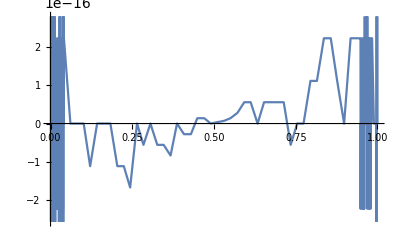

```mathematica
Plot[InverseErf[1-2 y]-InverseErfc[2 y],{y,0,1}]
```